```mathematica
Ν[d_, δ_] := ∫_-π^π ChebyshevT[d,(1+2*(Cos[x]-Cos[δ])/(1+Cos[δ]))]ⅆx
```

```mathematica
M[d_, δ_, x_] := 1/Ν[d, δ]*ChebyshevT[d,(1+2*(Cos[x]-Cos[δ])/(1+Cos[δ]))]
```

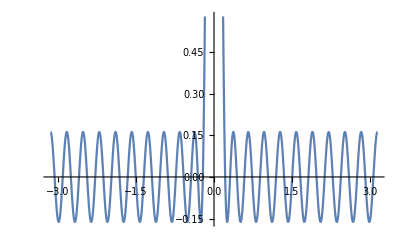

```mathematica
Plot[M[20,0.2,h],{h,-π,π}]
```

```mathematica
M̂[d_, δ_, k_]:= 1/(√(2*π))*∫_-π^π M[d, δ, x]*ⅇ^(-ⅈ*k*x) ⅆx
```

```mathematica
M̂[20, 0.2, 10]
```

0.283676+0. ⅈ